## The Square Well Potential

### 1. Solving the Schrodinger Equation

```mathematica
Subscript[V, 0] :=-2
a := 2
ℏ :=1
m :=1
```

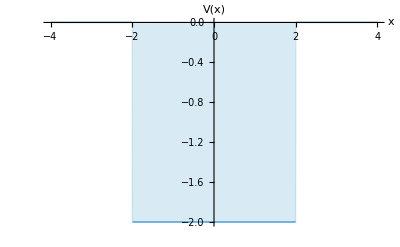

```mathematica
f[x_]:=Piecewise[{{0,x<-a},{Subscript[V,0],-a<=x<=a}}];
Plot[f[x],{x,-4,4},PlotStyle->Thick,AxesLabel->{"x","V(x)"},Filling->Axis]
```

#### Regions to the left and right of the barrier potential

The time-independent Schrodinger Equation has different forms in the regions to the left and right of the barrier potential:

#### First region x<0:

```mathematica
sol1 = DSolve[ Subscript[ψ, 1]''[x] == -(En^2-1) Subscript[ψ, 1][x],Subscript[ψ, 1][x],x];
TrigToExp[sol1]
```

{{ψ_1[x]→ⅇ^(√(1-En^2) x) C[1]+ⅇ^(-√(1-En^2) x) C[2]}}

Let k1 =  √(1-E^2)

```mathematica
Subscript[ψ, 1][x_] :=A Exp[k1 x] +B Exp[ -k1 x] /.{B->0}
```

#### Second Region -a<x>a

```mathematica
sol2= DSolve[ Subscript[ψ, 2]''[x] == -((En+V0)^2-1) Subscript[ψ, 2][x],Subscript[ψ, 2][x],x];
TrigToExp[sol2]
```

{{ψ_2[x]→ⅇ^(√(1-En^2-2 En V0-V0^2) x) C[1]+ⅇ^(-√(1-En^2-2 En V0-V0^2) x) C[2]}}

Let k2 =  √((E+V0)^2-1)

```mathematica
Subscript[ψ, 2][x_]:=C Exp[I k2 x]+ D Exp[-I k2 x]
```

#### Third Region x>a

```mathematica
sol3=DSolve[-ℏ^2/(2 m) Subscript[ψ, 3]''[x] == -En Subscript[ψ, 3][x],Subscript[ψ, 3][x],x];
TrigToExp[sol3]
```

{{ψ_3[x]→ⅇ^(√2 √En x) C[1]+ⅇ^(-√2 √En x) C[2]}}

```mathematica
Subscript[ψ, 3][x_]:=F Exp[k1 x]+G Exp[- k1 x]/.{F->0}
```

### 2. Getting the system of equations of Boundary Conditions

We apply the matching conditions for ψ(x) and ψ’(x), that is at the points x=-a and x=a, four equations in the arbitrary constants A, B, C, D, and F will be obtained:

```mathematica
eq1 = Subscript[ψ, 1][-a]==Subscript[ψ, 2][-a]
```

A ⅇ^(-2 k1)==C ⅇ^(-2 ⅈ k2)+D ⅇ^(2 ⅈ k2)

```mathematica
eq2 = Subscript[ψ, 2][a] == Subscript[ψ, 3][a]
```

D ⅇ^(-2 ⅈ k2)+C ⅇ^(2 ⅈ k2)==ⅇ^(-2 k1) G

```mathematica
eq3 = Subscript[ψ, 1]'[-a] == Subscript[ψ, 2]'[-a]
```

A ⅇ^(-2 k1) k1==ⅈ C ⅇ^(-2 ⅈ k2) k2-ⅈ D ⅇ^(2 ⅈ k2) k2

```mathematica
eq4 = Subscript[ψ, 2]'[a] == Subscript[ψ, 3]'[a]
```

-ⅈ D ⅇ^(-2 ⅈ k2) k2+ⅈ C ⅇ^(2 ⅈ k2) k2==-ⅇ^(-2 k1) G k1

### 3. Obtaining the Transcendental Equation

We add and subtract equations from the system of equations

```mathematica
eq5 = A Exp[-2 k1]+Exp[-2 k1] G==C Exp[-2 ⅈ k2]+D Exp[2 ⅈ k2]+D Exp[-2 ⅈ k2]+C Exp[2 ⅈ k2]//FullSimplify
```

ⅇ^(-2 k1) (A+G)==2 (C+D) Cos[2 k2]

```mathematica
eq6 = A ⅇ^(-2 k1) k1+ⅇ^(-2 k1) G k1==  ⅈ C ⅇ^(-2 ⅈ k2) k2-ⅈ D ⅇ^(2 ⅈ k2) k2-(-ⅈ D ⅇ^(-2 ⅈ k2) k2+ⅈ C ⅇ^(2 ⅈ k2) k2)//FullSimplify
```

ⅇ^(-2 k1) (A+G) k1==2 (C+D) k2 Sin[2 k2]

```mathematica
eq7 = (ⅇ^(-2 k1) (A+G) k1)/(ⅇ^(-2 k1) (A+G))==(2 (C+D) k2 Sin[2 k2])/(2 (C+D) Cos[2 k2])//FullSimplify
```

k1==k2 Tan[2 k2]

### 4. Finding the roots of the transcendental Equation

We implement a iterative method to find the roots for a range of values of V0

```mathematica
k1[En_?NumericQ]:=Sqrt[1-En^2];
k2[En_?NumericQ,V0_?NumericQ]:=Module[{s=(En+V0)^2-1},If[s>0,Sqrt[s],Indeterminate]];

(*even transcendental:k1=k2 Tan[a k2]*)
fEven[En_?NumericQ,V0_?NumericQ]:=Module[{k2v=k2[En,V0]},If[!NumericQ[k2v]||!(-1<En<1),Indeterminate,k1[En]-k2v Tan[a k2v]]];

(*-----FIRST even root only:enforce 0<a k2<π/2-----*)
firstEvenRoot[V0_?NumericQ,n_:2000]:=Module[{grid,vals,pairs,brackets},(*scan E from high->low so we pick the ground branch first*)grid=Subdivide[0.999999,-0.999999,n];
vals=Table[Module[{E=e,k2v=k2[e,V0],x},If[NumericQ[k2v],x=a k2v;
If[0<x<Pi/2&&NumericQ[Tan[x]],k1[E]-k2v Tan[x],Indeterminate],Indeterminate]],{e,grid}];
pairs=Partition[Transpose[{grid,vals}],2,1];
brackets=Select[pairs,VectorQ[#[[All,2]],NumericQ]&&Times@@Sign[#[[All,2]]]<0&];
If[brackets==={},Missing["NoRoot"],En/. FindRoot[fEven[En,V0]==0,{En,brackets[[1,1,1]],brackets[[1,2,1]]},(*first bracket->first branch*)Method->"Brent",MaxIterations->300]]];

(*sweep V0 and collect just that line*)
sweepFirstEven[vmin_:0.10,vmax_:2.05,dV_:0.05]:=Table[{V0,firstEvenRoot[V0]},{V0,N@Range[vmin,vmax,dV]}];

line=sweepFirstEven[0.10,2.05,0.05];
```

### 5. Plot Energy E vs Potential V0

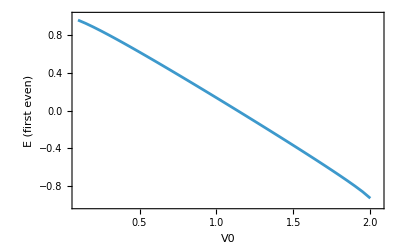

```mathematica
ListLinePlot[line,Frame->True,FrameLabel->{"V0","E (first even)"},PlotRange->{{0.1,2.05},{-1,1}}]
```

### 6. Table

```mathematica
tableWithHeader=Prepend[line,{"V0 ","E"}]//TableForm
```

V0  | E
0.1 | 0.958111
0.15 | 0.923159
0.2 | 0.884386
0.25 | 0.843163
0.3 | 0.800242
0.35 | 0.756079
0.4 | 0.71097
0.45 | 0.665115
0.5 | 0.618656
0.55 | 0.571698
0.6 | 0.524319
0.65 | 0.476578
0.7 | 0.428521
0.75 | 0.380183
0.8 | 0.331593
0.85 | 0.282774
0.9 | 0.233741
0.95 | 0.184509
1. | 0.135087
1.05 | 0.0854825
1.1 | 0.0356985
1.15 | -0.0142633
1.2 | -0.0644042
1.25 | -0.114728
1.3 | -0.165243
1.35 | -0.215959
1.4 | -0.26689
1.45 | -0.318057
1.5 | -0.369485
1.55 | -0.42121
1.6 | -0.473278
1.65 | -0.525754
1.7 | -0.578727
1.75 | -0.632326
1.8 | -0.686751
1.85 | -0.742331
1.9 | -0.799675
1.95 | -0.860169
2. | -0.928876
2.05 | Missing[NoRoot]

#### Norm of the Klein Gordon KG Equation

```mathematica
ClearAll[t,x,r,En,e,A0,V,ϕ,ψ,D0,dens];
ψ[t_,x_]:=Exp[-I En t] ϕ[x];
D0[f_]:=D[f,t]+I e A0[x] f;      

dens=Simplify[I (Conjugate[ψ[t,x]] D0[ψ[t,x]]-Conjugate[D0[ψ[t,x]]] ψ[t,x]),Assumptions->{En∈Reals,e∈Reals,A0[x]∈Reals}];

densV=dens//. {e A0[x]->V[x],Conjugate[t]->t};
densV//TraditionalForm
```

2 ϕ(x) Conjugate[ϕ(x)] (En-V(x))

```mathematica
Inactive[Integrate][2 (E-V[x]) Abs[ϕ[x]]^2,{x,-∞,∞}]
```

2 Abs[ϕ[x]]^2 (ⅇ-V[x])x-∞∞

#### Particle and Antiparticle Bound States

```mathematica
Clear[V0,En]
```

```mathematica
a=2;
V0=2.01;
En=0.940;
k1[E_]:=Sqrt[1-E^2];
k2[E_,V0_]:=Sqrt[(E+V0)^2-1];
```

```mathematica
Nsol=2 NIntegrate[En Cos[k2[En,V0] a]^2 Exp[2k1[En](a+x)],{x,-∞,-a}]+2NIntegrate[(En+V0) Cos[k2[En,V0] x]^2,{x,-a,a}]+2 NIntegrate[En Cos[k2[En,V0] a]^2 Exp[2 k1[En] (a-x)],{x,a,+∞} ]
```

13.7891

```mathematica
Clear[V0,En]
```

```mathematica
V0=2.01;
En=-0.999;
```

```mathematica
Nsol=2 NIntegrate[En Cos[k2[En,V0] a]^2 Exp[2k1[En](a+x)],{x,-∞,-a}]+2NIntegrate[(En+V0) Cos[k2[En,V0] x]^2,{x,-a,a}]+2 NIntegrate[En Cos[k2[En,V0] a]^2 Exp[2 k1[En] (a-x)],{x,a,+∞} ]
```

-32.9953